# DataTable

The DataTable package provides a representation of 1D data along with convenient manipulation functions.

```mathematica
SetDirectory[NotebookDirectory[]<>"/.."]
```

/Users/ian/Projects/Code/nrmma

```mathematica
<<"DataTable.m"
```

## Constructing

You can construct a DataTable object from a list of {x, f} pairs:

```mathematica
l=Table[{x,Sin[2Pi x]},{x,0,1,0.1}]
```

{{0.,0.},{0.1,0.587785},{0.2,0.951057},{0.3,0.951057},{0.4,0.587785},{0.5,1.22465×10^-16},{0.6,-0.587785},{0.7,-0.951057},{0.8,-0.951057},{0.9,-0.587785},{1.,-2.44929×10^-16}}

```mathematica
d=MakeDataTable[l]
```

DataTable[...]

x is the independent variable and f is the dependent variable.

The independent variable x should be monotonically increasing with a constant spacing.  The "range" of a DataTable is {x1, x2}, where x1 is the first and x2 is the last value of the independent variable.

DataTable objects print as "DataTable[...]" to avoid cluttering up a notebook display with all the data that you would see if you used lists directly.

## Using

A DataTable can be converted back to a list:

```mathematica
ToList[d]
```

{{0.,0.},{0.1,0.587785},{0.2,0.951057},{0.3,0.951057},{0.4,0.587785},{0.5,1.22465×10^-16},{0.6,-0.587785},{0.7,-0.951057},{0.8,-0.951057},{0.9,-0.587785},{1.,-2.44929×10^-16}}

Several Mathematica plotting routines have been extended to support DataTables:

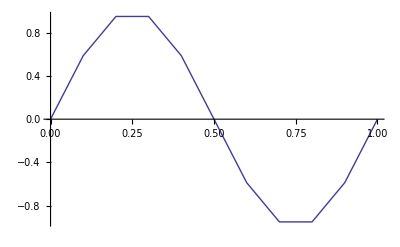

```mathematica
ListLinePlot[d]
```

You can perform arithmetic operations on DataTables with the same spacing and range:

```mathematica
d1=MakeDataTable[Table[{x,Sin[2Pi x]},{x,0,1,0.1}]]
```

DataTable[...]

```mathematica
d2=MakeDataTable[Table[{x,Cos[2Pi x]},{x,0,1,0.1}]]
```

DataTable[...]

```mathematica
d3=d1^2+d2^2
```

DataTable[...]

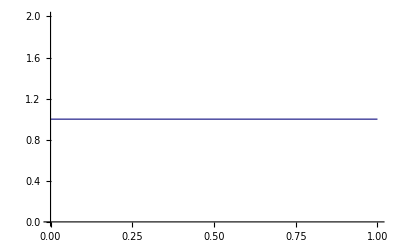

```mathematica
ListLinePlot[d3,PlotRange->{0,2}]
```

The full list of standard Mathematica functions which have been extended to work with DataTables is:

Arithmetic: Plus, Times, Dot, Power, Abs, Sqrt, Log
Complex:  Conjugate, Re, Im, 
List: Length,  First, Last, Take, Drop
Plotting: ListPlot, ListLinePlot, ListLogPlot
Vector: Norm
Misc: Interpolation

## Full API

The full list of DataTable function is below.  Click on one of them for documentation:

```mathematica
?DataTable`*
```